```mathematica
Clear["Global`*"]
```

```mathematica
coord={t,r,θ,φ};
metricsign=-1;
metric={{-1,0,0,0},{0,1,0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}};
Import["diffgeo.m"]
```

```mathematica
$Assumptions=Element[ϕ,Reals];
Φ[t_,r_]:=Exp[I ω t]ϕ[r];
SuperStar[Φ][t_,r_]:=Exp[-I ω t] ϕ[r];
```

```mathematica
V[Y_]:=λ(b*Y^2-a*Y^4+Y^6)/.{λ-> 1,a-> 2,b->1.1}
```

```mathematica
V[x]
```

1.1 x^2-2 x^4+x^6

```mathematica
1/2 D[V[x],x]//Simplify
```

3. (0.366667 x-1.33333 x^3+x^5)

```mathematica
FindMinimum[2*(1.1 x^2-2 x^4+x^6)/x^2,x]
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{0.2,{x→1.}}

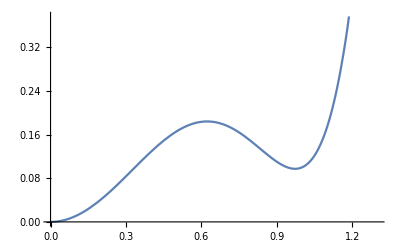

```mathematica
Plot[V[x],{x,0,1.3}]
```

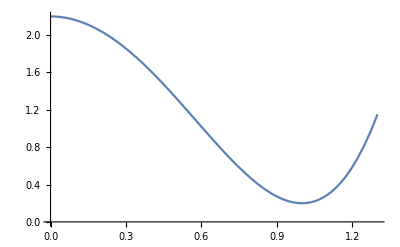

```mathematica
Plot[2*V[x]/x^2,{x,0,1.3}]
```

```mathematica
eq = scalarLaplacian[Φ[t,r]]+1/2 D[V[ϕ[r]],ϕ[r]]/.{Exp[I ω t]-> 1}//FullSimplify
```

(1.1+ω^2) ϕ[r]-4 ϕ[r]^3+3 ϕ[r]^5+(2 ϕ'[r])/r+ϕ''[r]

```mathematica
Solve[eq==0,ϕ''[r]]
```

{{ϕ''[r]→-(1.1+ω^2) ϕ[r]+4. ϕ[r]^3-3. ϕ[r]^5-(2. ϕ'[r])/r}}

```mathematica
eqcomp=eq /. ϕ-> (ϕ[#/(1+#)]&)/.{r-> ζ/(1-ζ)}//FullSimplify
```

(-1.1+ω^2) ϕ[ζ]+4. ϕ[ζ]^3-3. ϕ[ζ]^5+((1.-1. ζ)^4 (2. ϕ'[ζ]+1. ζ ϕ''[ζ]))/ζ

```mathematica
solphi =Solve[eqcomp==0,ϕ''[ζ]][[1,1]]//FullSimplify
```

ϕ''[ζ]→(1. (-1. (-1.1+ω^2) ϕ[ζ]-4. ϕ[ζ]^3+3. ϕ[ζ]^5-(2. (1.-1. ζ)^4 ϕ'[ζ])/ζ))/(1.-1. ζ)^4

```mathematica
eqphicom=ϕ''[ζ]/.solphi//Together//Simplify
```

(ζ (1.1-1. ω^2) ϕ[ζ]-4. ζ ϕ[ζ]^3+3. ζ ϕ[ζ]^5+(-2.+8. ζ-12. ζ^2+8. ζ^3-2. ζ^4) ϕ'[ζ])/((1.-1. ζ)^4 ζ)

```mathematica
D[eqphicom,ϕ[ζ]]
```

(ζ (1.1-1. ω^2)-12. ζ ϕ[ζ]^2+15. ζ ϕ[ζ]^4)/((1.-1. ζ)^4 ζ)

```mathematica
ff2=FortranForm[eqphicom//Together]/.{ϕ[ζ]-> z3,ϕ'[ζ]-> z4,ω-> z1,ζ->x}
```

```mathematica
ff23=FortranForm[D[eqphicom,ϕ[ζ]]//Together//FullSimplify]/.{ϕ[ζ]-> z3,ϕ'[ζ]-> z4,ω-> z1,ζ->x}
```

(1.1 - 1.*z1**2 - 12.*z3**2 + 15.*z3**4)/(1. - 1.*x)**4

```mathematica
ff24=FortranForm[D[eqphicom,ϕ'[ζ]]//Together//FullSimplify]/.{ϕ[ζ]-> z3,ϕ'[ζ]-> z4,ω-> z1,ζ->x}
```

-1.9999999999999996/x

```mathematica
ff21=FortranForm[D[eqphicom,ω]//Together//FullSimplify]/.{ϕ[ζ]-> z3,ϕ'[ζ]-> z4,ω-> z1,ζ->x}
```

(-2.*z1*z3)/(1. - 1.*x)**4

```mathematica
ff22=FortranForm[D[eqphicom,ω']//Together//FullSimplify]/.{ϕ[ζ]-> z3,ϕ'[ζ]-> z4,ω-> z1,ζ->x}
```

0

```mathematica
g4=Exp[-√(1-ω^2)r]/r;
```

```mathematica
g4comp=g4/.{r-> ζ/(1-ζ)}//FullSimplify
```

-(ⅇ^((ζ √(1-ω^2))/(-1+ζ)) (-1+ζ))/ζ

```mathematica
D[g4comp,ζ]
```

(ⅇ^((ζ √(1-ω^2))/(-1+ζ)) (-1+ζ))/ζ^2-(ⅇ^((ζ √(1-ω^2))/(-1+ζ)))/ζ-(ⅇ^((ζ √(1-ω^2))/(-1+ζ)) (-1+ζ) ((√(1-ω^2))/(-1+ζ)-(ζ √(1-ω^2))/(-1+ζ)^2))/ζ

```mathematica
psiasymp=Exp[-Ω*r]/r;
```

```mathematica
mud = psiasymp/.{r-> ζ/(1-ζ)}
```

(ⅇ^(-(ζ Ω)/(1-ζ)) (1-ζ))/ζ

(ⅇ^(-ζ/(1-ζ)) (1-ζ))/ζ

```mathematica
D[(ⅇ^(-(ζ Ω)/(1-ζ)) (1-ζ))/ζ,ζ]//Simplify
```

(ⅇ^((ζ Ω)/(-1+ζ)) (1+ζ (-1+Ω)))/((-1+ζ) ζ^2)

-(ⅇ^(-(ζ Ω)/(1-ζ)) (1-ζ))/ζ^2-ⅇ^(-(ζ Ω)/(1-ζ))/ζ+(ⅇ^(-(ζ Ω)/(1-ζ)) (1-ζ) (-Ω/(1-ζ)-(ζ Ω)/(1-ζ)^2))/ζ

ⅇ^(ζ/(-1+ζ))/((-1+ζ) ζ^2)

-(ⅇ^(-ζ/(1-ζ)) (1-ζ))/ζ^2-ⅇ^(-ζ/(1-ζ))/ζ+(ⅇ^(-ζ/(1-ζ)) (1-ζ) (-1/(1-ζ)-ζ/(1-ζ)^2))/ζ

(1.1 - 1.*z1**2 - 12.*z3**2 + 15.*z3**4)/(1. - 1.*x)**4

-1.9999999999999996/x

0

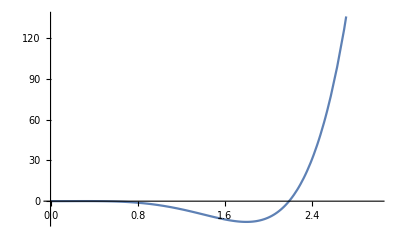

```mathematica
Plot[x^2-5 x^4+x^6,{x,0,3}]
```

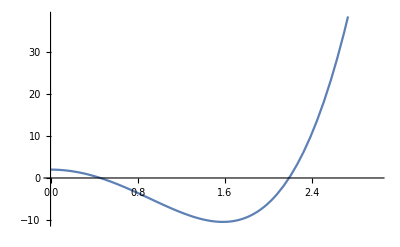

```mathematica
Plot[2*(x^2-5 x^4+x^6)/x^2,{x,0,3}]
```

```mathematica
Exp[-√(1-ω^2)r^2]/.{r-> ζ/(1-ζ)}
```

ⅇ^(-(ζ^2 √(1-ω^2))/(1-ζ)^2)

```mathematica
D[ⅇ^(-(ζ^2 √(1-ω^2))/(1-ζ)^2),ζ]//Simplify
```

(2 ⅇ^(-(ζ^2 √(1-ω^2))/(-1+ζ)^2) ζ √(1-ω^2))/(-1+ζ)^3

```mathematica
FortranForm[(2 ⅇ^(-(ζ^2 √(1-ω^2))/(-1+ζ)^2) ζ √(1-ω^2))/(-1+ζ)^3]/.{ζ-> x}
```

(2*x*Sqrt(1 - ω**2))/(E**((x**2*Sqrt(1 - ω**2))/(-1 + x)**2)*(-1 + x)**3)

```mathematica
√0.005
```

0.0707107

```mathematica
NIntegrate[x^2*Sin[x]^2*Cos[x]^3,{x,0,π}]
```

-0.726057

```mathematica
D[ⅇ^(-(ζ^2 √(1-ω^2))/(1-ζ)^2) (-(2 ζ √(1-ω^2))/(1-ζ)^2-(2 ζ^2 √(1-ω^2))/(1-ζ)^3),ζ]
```

```mathematica
ⅇ^(-(ζ^2 √(1-ω^2))/(1-ζ)^2) (-(2 √(1-ω^2))/(1-ζ)^2-(8 ζ √(1-ω^2))/(1-ζ)^3-(6 ζ^2 √(1-ω^2))/(1-ζ)^4)+ⅇ^(-(ζ^2 √(1-ω^2))/(1-ζ)^2) (-(2 ζ √(1-ω^2))/(1-ζ)^2-(2 ζ^2 √(1-ω^2))/(1-ζ)^3)^2//FullSimplify
```

(2 ⅇ^(-(ζ^2 √(1-ω^2))/(-1+ζ)^2) √(1-ω^2) (-1+ζ^2 (3-2 ζ+2 √(1-ω^2))))/(-1+ζ)^6

```mathematica
FortranForm[(2 ⅇ^(-(ζ^2 √(1-ω^2))/(-1+ζ)^2) √(1-ω^2) (-1+ζ^2 (3-2 ζ+2 √(1-ω^2))))/(-1+ζ)^6]/.{ζ-> x}
```

(2*Sqrt(1 - ω**2)*(-1 + x**2*(3 - 2*x + 2*Sqrt(1 - ω**2))))/(E**((x**2*Sqrt(1 - ω**2))/(-1 + x)**2)*(-1 + x)**6)

```mathematica
FortranForm[ⅇ^(-(ζ^2 √(1-ω^2))/(1-ζ)^2) (-(2 √(1-ω^2))/(1-ζ)^2-(8 ζ √(1-ω^2))/(1-ζ)^3-(6 ζ^2 √(1-ω^2))/(1-ζ)^4)+ⅇ^(-(ζ^2 √(1-ω^2))/(1-ζ)^2) (-(2 ζ √(1-ω^2))/(1-ζ)^2-(2 ζ^2 √(1-ω^2))/(1-ζ)^3)^2//FullSimplify]/.{ζ-> x}
```

(2*Sqrt(1 - ω**2)*(-1 + x**2*(3 - 2*x + 2*Sqrt(1 - ω**2))))/(E**((x**2*Sqrt(1 - ω**2))/(-1 + x)**2)*(-1 + x)**6)